```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergGerardCZDCSWAP.wl"]; 
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{1,1,0},{0,0,0},{1,0,0},{2,0,0},{0,1,0},{2,1,0},{0,2,0},{1,2,0},{2,2,0}}}](*,{1,2,0}}}]*),
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(*BlockadeRadius->3,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 98,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[Gates][[All,1]]
RydDev[InitLocations]
data=data=Import["/Users/questuser/Documents/Kathryn/BV3to9Q.csv"]; (*Imported gates from Qiskit*)
data[[5]];
d=data[[5]][[3;;data[[2,1]]+2]];
Length[data]
Fraction[a_,b_]:=a/b
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAP_(q1$_Integer,q2$_Integer),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$5208116,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$5208116[{p$,q$}],C_c$_[Z_t$__]/;blockadeCheck$5208116[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$5208116[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$5208116[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

-Graphics3D-

508

```mathematica
CircuitTranslator[DataSet_]:=Table[CircSplit=DataSet[[i,3;;DataSet[[i,1]]+2]];
(*Print[CircSplit];*)
Table[GateSplit=StringSplit[CircSplit[[j]],", ["];
GateName=StringTrim[StringTrim[GateSplit[[1]],"["],"'"];
GateQubits=IntegerPart[ToExpression[StringSplit[StringTrim[GateSplit[[2]],"]"],","]]];
GateParameters=If[StringContainsQ[GateName,"C"],Pi,Pi*ToExpression[StringReplace[StringTrim[GateSplit[[3]],"]]"],{"("->"[",")"->"]"}]]];
If[Length[GateQubits]==2,Subscript[ToExpression[GateName], GateQubits[[1]],GateQubits[[2]]][GateParameters],Subscript[ToExpression[GateName], GateQubits[[1]]][GateParameters]],{j,1,DataSet[[i,1]]}]
,{i,1,Length[DataSet]}]
(*a=data[[2;;Length[data]]][[1]][[3;;9]]*)
Table[DrawCircuit[(*ExtractCircuit[InsertCircuitNoise[*)CircuitTranslator[data][[i]](*,RydDev,ReplaceAliases->True]]*)],{i,1,Length[data]}]
```

```mathematica
{Subscript[Init, q$_Integer],Subscript[Wait, qubits$__][dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},Subscript[M, q$_Integer],Subscript[SRot, q$_Integer][ϕ$_,Δ$_,tg$_],Subscript[H, q$_Integer],Subscript[Rx, q$_Integer][θ$_],Subscript[Ry, q$_Integer][θ$_],Subscript[Rz, q$_Integer][θ$_],Subscript[SWAP, q1$_Integer,q2$_Integer],Subscript[SWAPLoc, q1$_Integer,q2$_Integer],Subscript[ShiftLoc, q$__][v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1852814,v$],Subscript[CZ, p$_Integer,q$_Integer][ϕ$_]/;blockadeCheck$1852814[{p$,q$}],Subscript[C, c$_][Subscript[Z, t$__]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$_][Subscript[Z, t$__][θ$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_][θ$_]]}
```

```mathematica
KetList[NQ_]:=Table[IntegerString[i,2,4],{i,0,2^NQ-1,1}]
KetList[4]
Length[%]
```

{0000,0001,0010,0011,0100,0101,0110,0111,1000,1001,1010,1011,1100,1101,1110,1111}

16

```mathematica
{"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

16

```mathematica
percent2infidel[num_]:=Module[{},Assert[0<=num<=100,"number is in percent"];1-0.01 num];
Circs=CircuitTranslator[data];
Meas[q_]:={Subscript[Depol, q][1-0.01*99.7] };
(*BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[InitZeroState[ρ];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]*)
BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[NShots=2000;InitZeroState[ρ];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];
MeasCirc=ExtractCircuit[InsertCircuitNoise[Table[Subscript[M, i],{i,1,Nq-1}],RydDev,ReplaceAliases->True]];
ProbMeas=Table[ρClone=CreateDensityQureg[9];CloneQureg[ρClone,ρ];ApplyCircuit[ρClone,MeasCirc];A=CalcProbOfAllOutcomes[ρClone,Range[1,Nq-1]];DestroyQureg[ρClone];A,{j,1,NShots}];
{Mean[ProbMeas],2*StandardDeviation[ProbMeas]/Sqrt[NShots]},{i,1,Length[Circs]}]
ρ=CreateDensityQureg[9];
i=1
Table[Probs=BVCircuitApplier[Circs[[i;;i+2^(Nq-1)-1]],ρ,Nq];i=i+2^(Nq-1);Probs,{Nq,3,9}]

DestroyAllQuregs[];
```

1

```mathematica
x=Range[0,2^4];
y=Range[0,2^4];
Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Resultant State","Input Seed","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]
```

-Graphics3D-

```mathematica
?CalcProbOfAllOutcomes
```

```mathematica
?QuEST`*
```

```mathematica
BVData=
```

```mathematica
BVDataMeas=;
```

```mathematica
Flatten[BVDataMeas[[1]],1][[;;;;2]]
```

{{0.951,0.016,0.0145,0.000153148},{0.0165,0.9475,0.0005,0.0126518},{0.014,0.0005,0.9395,0.0163938},{0.,0.0135,0.0115,0.949423}}

```mathematica
AvgProbs=Table[Res=BVData[[i]];x=Range[0,2^(i+1)];
y=Range[0,2^(i+1)];
Print[Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Resultant State","Input Seed","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]];μ=(Total[Diagonal[Res]]/Length[Res]); {i+1,μ±2*StandardDeviation[Diagonal[Res]]/Sqrt[Length[Res]]},{i,1,7}]
ListLinePlot[AvgProbs,Frame->True,FrameLabel->{Style["Number of Data Qubits",16],Style["P_Seed",16]}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

{{2,0.946856±0.00510844},{3,0.931585±0.00317002},{4,0.911382±0.00390118},{5,0.890598±0.00268071},{6,0.872172±0.00186668},{7,0.851971±0.00178763},{8,0.833735±0.00114099}}

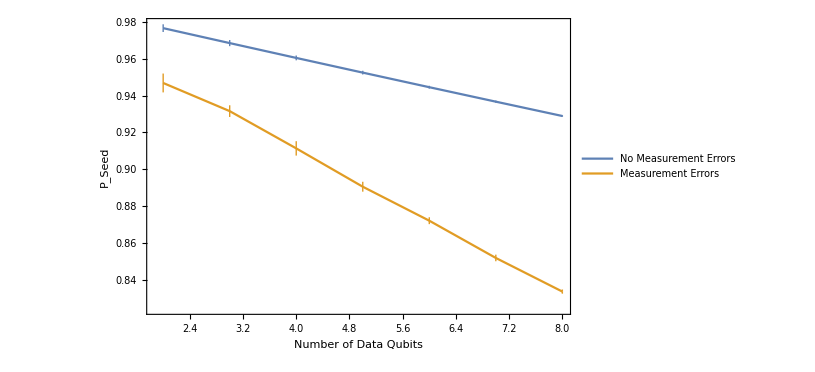

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

{{2,0.976585±0.00209034},{3,0.968479±0.0016629},{4,0.96044±0.00130145},{5,0.952466±0.00100424},{6,0.944559±0.000765646},{7,0.936716±0.000577909},{8,0.928938±0.000432589}}

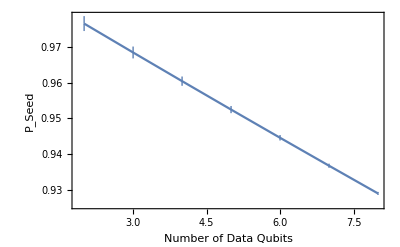

```mathematica
AvgProbsMeas=Table[Res=Flatten[BVDataMeas[[i]],1][[;;;;2]];x=Range[0,2^(i+1)];
y=Range[0,2^(i+1)];
Print[Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Resultant State","Input Seed","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]];μ=(Total[Diagonal[Res]]/Length[Res]); {i+1,μ±2*StandardDeviation[Diagonal[Res]]/Sqrt[Length[Res]]},{i,1,7}]
ListLinePlot[{AvgProbs,AvgProbsMeas},Frame->True,FrameLabel->{Style["Number of Data Qubits",16],Style["P_Seed",16]},PlotLegends->{"No Measurement Errors","Measurement Errors"}]
```

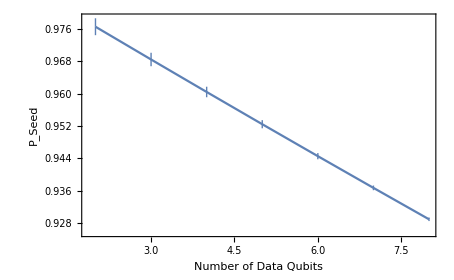
```mathematica
(*No Measurement Error Results*)
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
{{2,0.9765854657134726±0.002090341476525771},{3,0.9684793102039445±0.0016628958486458933},{4,0.9604398306356077±0.0013014515488974673},{5,0.9524664836818113±0.0010042402245441318},{6,0.9445587304009228±0.0007656464089475579},{7,0.9367160362012865±0.0005779085548974236},{8,0.9289378708064617±0.0004325890822758662}}
-Graphics-
```